```mathematica
Clear["Global`*"]; 
SetDirectory[NotebookDirectory[]]
```

C:\Users\irisp\Documents\these\chapitre_3\mathematica\final version

# Analyses for the coevolution of helping and socially-mediated helping

## 0. Required functions

```mathematica
Pk0[k_,z_,n_]:=PDF[BinomialDistribution[n,z],k](* Probability that there is k cooperators among n individuals when the population is monomorphic for z *)
fec[k_,j_]:=(1+δ (Bc[k]/n-Cc j)) (* fecundity of an individual either cooperating (j=1) or defecting (j=0) in a group with k cooperators *)
fecpatch[k_]:=(1+ δ((k /n)(Bc[k]/n-Cc )+(1-k/n)(Bc[k]/n)));
(* average fecundity in a patch with k cooperators*)
fecphilo[k_]:=fecpatch[k](1-d[k]);(* offspring produced that will remain in their local patch *)
fecdisp[z_]:= ∑_(k2=0)^n d[k2] (1-cd) fecpatch[k2]Pk0[k2,z,n];
(* number of offspring coming into an arbirary patch when the population is monomorphic for z *)

w=∑_(c0=0)^(n-3) ∑_(c3=0)^1 ∑_(c2=0)^1 ∑_(c1=0)^1 fec[c1+c2+c3+c0,c1]((  1-d[1,c1+c2+c3+c0])/(( (1-d[1,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c1]/n+ (1-d[2,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c2]/n+(1-d[3,c1+c2+c3+c0])fec[c1+c2+c3+c0,c3]/n+(1-d[c1+c2+c3+c0]) ((n-3-c0)fec[c1+c2+c3+c0,0]/n+c0 fec[c1+c2+c3+c0,1]/n) )+ fecdisp[d[n+1]]) + ∑_(k0=0)^n ((d[1,c1+c2+c3+c0](1-cd) )/( fecphilo[k0]+ fecdisp[d[n+1]]))Pk0[k0,d[n+1],n])d[1,n+1]^c1(1-d[1,n+1])^(1-c1) d[2,n+1]^c2(1-d[2,n+1])^(1-c2)d[3,n+1]^c3(1-d[3,n+1])^(1-c3) Pk0[c0,d[n+1],n-3];
(* Fitness of a focal individual*)
wmono[k_,z_,j_]:=fec[k,j]((  1-d[k])/(fecpatch[k](1-d[k])+ fecdisp[z]) + ∑_(kd=0)^n (d[k](1-cd))/(fecphilo[kd]+ fecdisp[z])Pk0[kd,z,n]);
(*fitness of an invididual either helping or defecting in a patch with k helpers, when the entire population expresses z *)

wNeutral[k_,z_]:=((  1-d[k])/(fecpatch[k](1-d[k])+ fecdisp[z]) + ∑_(kd=0)^n (d[k](1-cd))/(fecphilo[kd]+ fecdisp[z])Pk0[kd,z,n])/.δ->0;
(*fitness of an invididual in a patch with k helpers, when the entire population expresses z but helping has no effect on fitness *)

m[k_]:=fecdisp[z]/(fecpatch[k](1-d[k])+fecdisp[z])/.δ->0;(* number of individual that are migrants in a patch that had k cooperators at the last generation /!\ only true when δ is small *)
nval= 4;
(* For mathematica to be able to solve functions using sums over k, we need to define an arbitrary value of n *)
monopop=Flatten[Table[{ d[i,k]-> d[k]},{k,0,nval+1},{i,1,3}]];
(*This table allows us to evaluate functions when the population is monomorphic *)
uncond1=Flatten[Table[{ d[i,k]-> d[i,0]},{k,0,nval},{i,1,3}]];
uncond2=Flatten[Table[{ d[k]-> d[0]},{k,0,nval} ]];
(*These vectors allows us to evaluate functions when dispersal is not socially-mediated (when all dispersal traits are equal to the dispersal probability when k=0)*)
R2 == ∑_(k =0)^n (1-m[k])^2(1/n+(n-1)/n R2)Pk0[k,z,n]/.n->nval/.δ->0;
solR2=Flatten[Solve[%,R2]];
solR2Uncondi=solR2/.uncond2//FullSimplify;
R2R == ∑_(k =0)^n (1/n+(n-1)/n(1-m[k])^2 R2R)Pk0[k,z,n]/.n->nval/.δ->0;
solR2R=Flatten[Solve[%,R2R]];
solR2RUncondi=solR2R/.uncond2//FullSimplify;
d0baseline=2/(1+2 cd n+√(1+4 cd^2 (-1+n) n))/.n->nval;
```

## 1. Selection on cooperation

Here we derive the conditions for cooperative strategies to invade a population of full defectors.  These results are presented in Appendix C.1, and in section 3.1 of the main text.

### 1.1. Direct fitness effect

```mathematica
Dwi=D[w,d[1,n+1]]/.n->nval/.monopop/. d[5]->0//FullSimplify; 
%==wmono[1,z,1]-1/.n->nval/.z->0//FullSimplify
(*eq. C-5*)
```

True

```mathematica
Normal[Series[Evaluate[D[w,d[1,n+1]]/.n->nval/.monopop/. d[5]->0],{δ,0,1}]]/.δ ->1/.Bc[0] ->0//FullSimplify;
%==(wNeutral[1,z]-1)- Cc (wNeutral[1,z]-(1-m[1])^2/n)+ (Bc[1]/n) (wNeutral[1,z]-(1-m[1])^2 )/.n->nval/.z->0/. d[5]->0//FullSimplify  (*eq. C-7*)
```

True

```mathematica
wNeutral[1,z]-1==(1-d[1])/(1-d[1]+(1-cd) d[0])+((1-cd) d[1])/(1-cd d[0])-1/.n->nval/.z->0//FullSimplify
 (*eq. C-8*)
```

True

### 1.2. Indirect fitness effect

```mathematica
Dwj=D[w,d[2,n+1]]/.n->nval/.monopop/. d[5]->0//FullSimplify;
%==wmono[1,z,0]-1/.n->nval/.z->0//FullSimplify
(*eq C-13*)
```

True

```mathematica
Normal[Series[Evaluate[D[w,d[2,n+1]]/.n->nval/.monopop/. d[5]->0],{δ,0,1}]]/.δ ->1/.Bc[0] ->0//FullSimplify;
%==(wNeutral[1,z]-1)+Cc(1-m[1])^2/n+ (Bc[1]/n) (wNeutral[1,z]-(1-m[1])^2 )/.n->4/.z->0/. d[5]->0//FullSimplify
(*eq C-14*)
```

True

### 1.3. The selection gradient

```mathematica
sz=Dwi+(n -1)R2 Dwj/.solR2/.z->0/.d[5]->0;
```

```mathematica
szWeakSel=Normal[Series[Evaluate[sz/.n->nval],{δ,0,1}]]/.solR2/.z->0/.d[5]->0/.δ ->1/.Bc[0] ->0;
%==n R2R(wNeutral[1,z]-1)-Cc (wNeutral[1,z]-  R2R(1-m[1])^2)+Bc[1]  (R2R wNeutral[1,z]- R2R(1-m[1])^2 )/.n->nval/.solR2R/.solR2/.z->0/.d[5]->0/.Bc[0] ->0//FullSimplify
(*eq C-15*)
```

True

#### 1.3.a In the presence of socially - mediated dispersal

```mathematica
szWeakSel==(A+(n-1)/n Bc[1]κ-Cc+ Bc[1]/n)(wNeutral[1,z]-R2R(1-m[1])^2)/.A->n R2R(wNeutral[1,z]-1)/((wNeutral[1,z])-R2R(1-m[1])^2)/.κ->(R2 (wNeutral[1,z])- R2R (1-m[1])^2)/((wNeutral[1,z])-R2R(1-m[1])^2)/.n->nval/.solR2R/.solR2/.z->0/.d[5]->0/.Bc[0] ->0//FullSimplify
(*eq C-16 to eq. C-19*)
```

True

#### 1.3.b In the absence of socially - mediated dispersal

```mathematica
(wNeutral[1,z]-R2R(1-m[1])^2)==1-R2/.n->nval/.solR2R/.solR2/.z->0/.d[5]->0/.Bc[0] ->0/.uncond1/.uncond2//FullSimplify (*C-21*)
```

True

```mathematica
A/.A->n R2R(wNeutral[1,z]-1)/((wNeutral[1,z])-R2R(1-m[1])^2)/.n->nval/.solR2R/.solR2/.z->0/.d[5]->0/.Bc[0] ->0/.uncond1/.uncond2//FullSimplify (*C-22*)
```

0

```mathematica
κ/.κ->(R2 (wNeutral[1,z])- R2R (1-m[1])^2)/((wNeutral[1,z])-R2R(1-m[1])^2)/.n->nval/.solR2R/.solR2/.z->0/.d[5]->0/.Bc[0] ->0/.uncond1/.uncond2//FullSimplify (*C-23*)
```

0

```mathematica
szWeakSel/.n->nval/.solR2R/.solR2/.z->0/.d[5]->0/.Bc[0] ->0/.uncond1/.uncond2//FullSimplify;
%==(- Cc+Bc[1]/n)(1-R2)/.solR2/.n->nval/.uncond1/.uncond2//FullSimplify
(*only the direct effect of cooperation determines whether cooperation can invade or not when dispersal is unconditional (in line with Taylor 1992)*)
```

True

### 1.4. Figure 2

```mathematica
(* Here we define a function that shows the range of Subscript[d, 1] and Subscript[c, d] for which socially-mediated dispersal favours the invasion of cooperators. We define it such that it draws such figure for any group size n*)
```

```mathematica
MakeplotInvade[n_]:=(grey=RGBColor["#878E88"];
yellow= RGBColor["#F7CB15"];
violet=RGBColor["#B989A9"];
darkviolet=RGBColor["#885075"];
red=RGBColor["#C71F1F"];
lightred=RGBColor["#f27c7c"];
cm=72/2.54;
monopop=Flatten[Table[{ d[i,k]-> d[k]},{k,0,n+1},{i,1,3}]];
(*This table allows us to evaluate functions when the population is monomorphic *)
uncond1=Flatten[Table[{ d[i,k]-> d[i,0]},{k,0,n},{i,1,3}]];
uncond2=Flatten[Table[{ d[k]-> d[0]},{k,0,n} ]];
(*Those functions allows us to evaluate functions when dispersal is not socially-mediated (when all dispersal traits are equal to the dispersal probability when k=0)*)
Pk0[k_,z_]:=z^k(1-z)^(n-k)Binomial[n,k];
fec[k_,j_]:=(1+δ (Bc[k]/n-Cc j)) (* fecundity of an individual either cooperating (j=1) or defecting (j=0) in a group with k cooperators *);
fecpatch[k_]:=(1+ δ((k /n)(Bc[k]/n-Cc )+(1-k/n)(Bc[k]/n)));
(* average fecundity in a patch with k cooperators*)
fecphilo[k_]:=fecpatch[k](1-d[k]);(* offspring produced that will remain in their local patch *)
fecdisp[z_]:= ∑_(k2=0)^n d[k2] (1-cd) fecpatch[k2]Pk0[k2,z];
m[k_]:=fecdisp[z] /(fecpatch[k](1-d[k])+fecdisp[z] )/.δ->0;
solR2=Flatten[Solve[R2 == ∑_(k =0)^n (1-m[k])^2(1/n+((n-1)/n)R2)Pk0[k,z]/.δ->0,R2]];
solR2Uncondi=solR2/.uncond2//FullSimplify;
solR2R=Flatten[Solve[R2R == ∑_(k =0)^n (1/n+((n-1)/n)(1-m[k])^2 R2R)Pk0[k,z]/.δ->0,R2R]];
solR2RUncondi=solR2R/.uncond2//FullSimplify;
d0baseline=2/(1+2 cd n+√(1+4 cd^2 (-1+n) n));
wNeutral[k_,z_]:=((  1-d[k])/( fecpatch[k](1-d[k])+ fecdisp[z]) + ∑_(kd=0)^n ((d[k](1-cd) )/( fecphilo[kd]+ fecdisp[z]))Pk0[kd,z])/.δ->0;
A=n R2R((wNeutral[1,z]-1)/((wNeutral[1,z])-R2R(1-m[1])^2))/.solR2R/.solR2/.z->0/.d[n+1]->0/.d[1]->Subscript[d, 1]/.d[0]->d0baseline;
κ= ( R2 (wNeutral[1,z])- R2R (1-m[1])^2)/((wNeutral[1,z])-R2R(1-m[1])^2)/.solR2R/.solR2/.z->0/.d[n+1]->0/.d[1]->Subscript[d, 1]/.d[0]->d0baseline/.Bc[0] ->0;
p1=RegionPlot[A>0,{cd,0,1},{Subscript[d, 1],0,1},Mesh->50,MeshFunctions->{#1-#2&},MeshShading->{yellow,None},BoundaryStyle->None] ;
p2=RegionPlot[κ>0,{cd,0,1},{Subscript[d, 1],0,1},PlotStyle->Directive[grey],BoundaryStyle->None] ;
p3=ContourPlot[Evaluate[Subscript[d, 1]== d0baseline] ,{cd,0,1},{Subscript[d, 1],0,1},ContourStyle->{Thick,Red}];
plotfinal=Show[p2,p1,p3,FrameLabel->{"dispersal cost, c_d"," "},LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black,ImageSize->10 cm],FrameTicks->{{{0,.5,1},None},{{0,.5,1},None}}])
```

```mathematica
P2=Show[MakeplotInvade[2],FrameLabel->{"dispersal cost, c_d","dispersal with one cooperator, d_1"}];
P4=MakeplotInvade[4];
P20=MakeplotInvade[20];
```

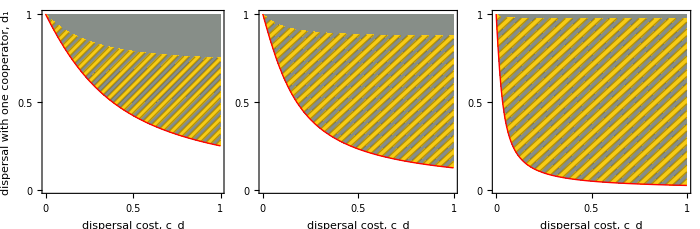

RegioPlotsB1.pdf

```mathematica
GraphicsRow[{P2,P4,P20},Spacings->0,ImageSize->700]
Export["RegioPlotsB1.pdf",Show[%]]
```

## 2. Selection on defection

Here we derive the conditions for  cooperation to be maintained, or equivalently, the conditions under which defection cannot invade a population of full cooperators.  These results are presented in Appendix C.2.

```mathematica
Clear["Global`*"]; 
SetDirectory[NotebookDirectory[]]
```

C:\Users\irisp\Documents\these\chapitre_3\mathematica\final version

### 2.0. Required functions

```mathematica
Pk0[k_,z_,n_]:=PDF[BinomialDistribution[n,z],k](* Probability that there is k cooperators among n individuals when the population is monomorphic for z *)
fec[k_,j_]:=(1+δ (Bc[k]/n-Cc j)) (* fecundity of an individual either cooperating (j=1) or defecting (j=0) in a group with k cooperators *)
fecpatch[k_]:=(1+ δ((k /n)(Bc[k]/n-Cc )+(1-k/n)(Bc[k]/n)));
(* average fecundity in a patch with k cooperators*)
fecphilo[k_]:=fecpatch[k](1-d[k]);(* offspring produced that will remain in their local patch *)
fecdisp[z_]:= ∑_(k2=0)^n d[k2] (1-cd) fecpatch[k2]Pk0[k2,z,n];
(* number of offspring coming into an arbirary patch when the population is monomorphic for z *)

w=∑_(c0=0)^(n-3) ∑_(c3=0)^1 ∑_(c2=0)^1 ∑_(c1=0)^1 fec[c1+c2+c3+c0,c1]((  1-d[1,c1+c2+c3+c0])/(( (1-d[1,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c1]/n+ (1-d[2,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c2]/n+(1-d[3,c1+c2+c3+c0])fec[c1+c2+c3+c0,c3]/n+(1-d[c1+c2+c3+c0]) ((n-3-c0)fec[c1+c2+c3+c0,0]/n+c0 fec[c1+c2+c3+c0,1]/n) )+ fecdisp[d[n+1]]) + ∑_(k0=0)^n ((d[1,c1+c2+c3+c0](1-cd) )/( fecphilo[k0]+ fecdisp[d[n+1]]))Pk0[k0,d[n+1],n])d[1,n+1]^c1(1-d[1,n+1])^(1-c1) d[2,n+1]^c2(1-d[2,n+1])^(1-c2)d[3,n+1]^c3(1-d[3,n+1])^(1-c3) Pk0[c0,d[n+1],n-3];
(* Fitness of a focal individual*)
wmono[k_,z_,j_]:=fec[k,j]((  1-d[k])/(fecpatch[k](1-d[k])+ fecdisp[z]) + ∑_(kd=0)^n (d[k](1-cd))/(fecphilo[kd]+ fecdisp[z])Pk0[kd,z,n]);
(*fitness of an invididual either helping or defecting in a patch with k helpers, when the entire population expresses z *)

wNeutral[k_,z_]:=((  1-d[k])/(fecpatch[k](1-d[k])+ fecdisp[z]) + ∑_(kd=0)^n (d[k](1-cd))/(fecphilo[kd]+ fecdisp[z])Pk0[kd,z,n])/.δ->0;
(*fitness of an invididual in a patch with k helpers, when the entire population expresses z but helping has no effect on fitness *)

m[k_]:=fecdisp[z]/(fecpatch[k](1-d[k])+fecdisp[z])/.δ->0;(* number of individual that are migrants in a patch that had k cooperators at the last generation /!\ only true when δ is small *)
nval= 4;
(* For mathematica to be able to solve functions using sums over k, we need to define an arbitrary value of n *)
monopop=Flatten[Table[{ d[i,k]-> d[k]},{k,0,nval+1},{i,1,3}]];
(*This table allows us to evaluate functions when the population is monomorphic *)
uncond1=Flatten[Table[{ d[i,k]-> d[i,0]},{k,0,nval},{i,1,3}]];
uncond2=Flatten[Table[{ d[k]-> d[0]},{k,0,nval} ]];
(*These vectors allows us to evaluate functions when dispersal is not socially-mediated (when all dispersal traits are equal to the dispersal probability when k=0)*)
R2 == ∑_(k =0)^n (1-m[k])^2(1/n+(n-1)/n R2)Pk0[k,z,n]/.n->nval/.δ->0;
solR2=Flatten[Solve[%,R2]];
solR2Uncondi=solR2/.uncond2//FullSimplify;
R2R == ∑_(k =0)^n (1/n+(n-1)/n(1-m[k])^2 R2R)Pk0[k,z,n]/.n->nval/.δ->0;
solR2R=Flatten[Solve[%,R2R]];
solR2RUncondi=solR2R/.uncond2//FullSimplify;
d0baseline=2/(1+2 cd n+√(1+4 cd^2 (-1+n) n))/.n->nval;
```

### 2.1. Direct fitness effect

```mathematica
Dwi=D[w,d[1,n+1]]/.n->nval/.monopop/. d[5]->1//FullSimplify;
%==1-wmono[n-1,z,0]/.n->nval/.z->1//FullSimplify
(*eq. C-24*)
```

True

```mathematica
Normal[Series[Evaluate[D[w,d[1,n+1]]/.n->nval/.monopop/. d[5]->1],{δ,0,1}]]/.δ ->1/.Bc[0] ->0//FullSimplify;
%==(1-wNeutral[n-1,z])+ (ΔB/n) (wNeutral[n-1,z]-(1-m[n-1])^2)-Cc (wNeutral[n-1,z]- (1-m[n-1])^2/n)/.ΔB->Bc[n]-Bc[n-1]/.n->nval/.z->1/. d[5]->1//FullSimplify
(*eq. C-26*)
```

True

```mathematica
(1-wNeutral[n-1,z])/.n->nval/.z->1/. d[5]->1//FullSimplify;
%==1-(1-d[n-1])/(1-d[n-1]+(1-cd) d[n])-((1-cd) d[n-1])/(1-cd d[n])/.n->nval//FullSimplify
(*eq. C-27*)
```

True

### 2.2. Indirect fitness effect

```mathematica
Dwj=D[w,d[2,n+1]]/.n->4/.monopop/. d[5]->1//FullSimplify;
%==1-wmono[n-1,z,1]/.n->4/.z->1//FullSimplify
(*eq. C-28*)
```

True

```mathematica
Normal[Series[Evaluate[D[w,d[2,n+1]]/.n->4/.monopop/. d[5]->1],{δ,0,1}]]/.δ ->1/.Bc[0] ->0//FullSimplify;
%==(1-wNeutral[n-1,z])+Cc (1-m[n-1])^2/n+ ΔB/n (wNeutral[n-1,z]-(1-m[n-1])^2)/.ΔB->Bc[n]-Bc[n-1]/.n->4/.z->1/. d[5]->1//FullSimplify
(*eq. C-29*)
```

True

### 2.3. The selection gradient

```mathematica
sz=Dwi+(n -1)R2 Dwj/.solR2/.z->1/.d[5]->1;
```

```mathematica
szWeakSel=Normal[Series[Evaluate[sz/.n->nval],{δ,0,1}]]/.solR2/.z->1/.d[5]->1/.δ ->1;
%==n R2R(1-wNeutral[n-1,z]) + ΔB   (R2R wNeutral[n-1,z]- R2R (1-m[n-1])^2 )- Cc (wNeutral[n-1,z]-R2R (1-m[n-1])^2)/.ΔB->Bc[n]-Bc[n-1]/.n->nval/.solR2R/.solR2/.z->1/.d[5]->1//FullSimplify
(*eq. C-30*)
```

True

```mathematica
szWeakSel==(wNeutral[n-1,z]-R2R(1-m[n-1])^2)(A+(n-1)/n ΔB κ -Cc+ ΔB/n)/.A->n R2R(1-wNeutral[n-1,z])/((wNeutral[n-1,z])-R2R(1-m[n-1])^2)/.κ->(R2 (wNeutral[n-1,z])- R2R (1-m[n-1])^2)/((wNeutral[n-1,z])-R2R(1-m[n-1])^2)/.ΔB->Bc[n]-Bc[n-1]/.n->nval/.solR2R/.solR2/.z->1/.d[5]->1/.Bc[0] ->0//FullSimplify//FullSimplify
(*eq C-31 to C-34*)
```

True

### 2.4. Figure S1-2

```mathematica
MakeplotMaintain[n_]:=(grey=RGBColor["#878E88"];
yellow= RGBColor["#F7CB15"];
violet=RGBColor["#B989A9"];
darkviolet=RGBColor["#885075"];
red=RGBColor["#C71F1F"];
lightred=RGBColor["#f27c7c"];
cm=72/2.54;
monopop=Flatten[Table[{ d[i,k]-> d[k]},{k,0,n+1},{i,1,3}]];
(*This table allows us to evaluate functions when the population is monomorphic *)
uncond1=Flatten[Table[{ d[i,k]-> d[i,0]},{k,0,n},{i,1,3}]];
uncond2=Flatten[Table[{ d[k]-> d[0]},{k,0,n} ]];
(*Those functions allows us to evaluate functions when dispersal is not socially-mediated (when all dispersal traits are equal to the dispersal probability when k=0)*)
Pk0[k_,z_]:=z^k(1-z)^(n-k)Binomial[n,k];
fec[k_,j_]:=(1+δ (Bc[k]/n-Cc j)) (* fecundity of an individual either cooperating (j=1) or defecting (j=0) in a group with k cooperators *);
fecpatch[k_]:=(1+ δ((k /n)(Bc[k]/n-Cc )+(1-k/n)(Bc[k]/n)));
(* average fecundity in a patch with k cooperators*)
fecphilo[k_]:=fecpatch[k](1-d[k]);(* offspring produced that will remain in their local patch *)
fecdisp[z_]:= ∑_(k2=0)^n d[k2] (1-cd) fecpatch[k2]Pk0[k2,z];
m[k_]:=fecdisp[z]/(fecpatch[k](1-d[k])+fecdisp[z])/.δ->0;
solR2=Flatten[Solve[R2 == ∑_(k =0)^n (1-m[k])^2(1/n+(n-1)/n R2)Pk0[k,z]/.δ->0,R2]];
solR2Uncondi=solR2/.uncond2//FullSimplify;
solR2R=Flatten[Solve[R2R == ∑_(k =0)^n (1/n+(n-1)/n(1-m[k])^2 R2R)Pk0[k,z]/.δ->0,R2R]];
solR2RUncondi=solR2R/.uncond2//FullSimplify;
d0baseline=2/(1+2 cd n+√(1+4 cd^2 (-1+n) n));
wNeutral[k_,z_]:=((  1-d[k])/(fecpatch[k](1-d[k])+ fecdisp[z]) + ∑_(kd=0)^n (d[k](1-cd))/(fecphilo[kd]+ fecdisp[z])Pk0[kd,z])/.δ->0;
A=n R2R(1-wNeutral[n-1,z])/((wNeutral[n-1,z])-R2R(1-m[n-1])^2)/.solR2R/.solR2/.z->1/.d[n+1]->1/.d[n-1]->Subscript[d, n-1]/.d[n]->d0baseline;

K= (R2 (wNeutral[n-1,z])- R2R (1-m[n-1])^2)/((wNeutral[n-1,z])-R2R(1-m[n-1])^2)/.solR2R/.solR2/.z->1/.d[n+1]->1/.d[n-1]->Subscript[d, n-1]/.d[n]->d0baseline/.Bc[0] ->0;
p1=RegionPlot[A>0,{cd,0,1},{Subscript[d, n-1],0,1},Mesh->50,MeshFunctions->{#1-#2&},MeshShading->{yellow,None},BoundaryStyle->None] ;
p2=RegionPlot[K>0,{cd,0,1},{Subscript[d, n-1],0,1},PlotStyle->Directive[grey],BoundaryStyle->None] ;
p3=ContourPlot[Evaluate[Subscript[d, n-1]== d0baseline] ,{cd,0,1},{Subscript[d, n-1],0,1},ContourStyle->{Thick,Red}];
plotfinal=Show[p2,p1,p3,FrameLabel->{None,None},LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black,ImageSize->10 cm],FrameTicks->{{{0,.5,1},None},{{0,.5,1},None}}])
```

```mathematica
P2=Show[MakeplotMaintain[2],FrameLabel->{None,None}];
P4=MakeplotMaintain[4];
P10=MakeplotMaintain[20];
```

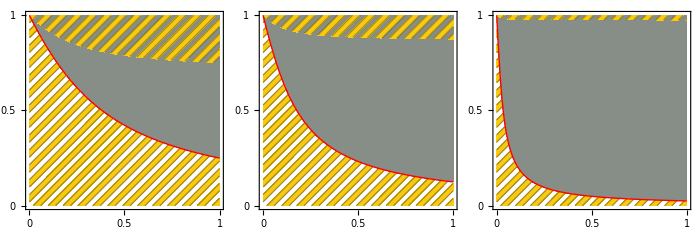

RegioPlots_cheat.pdf

```mathematica
GraphicsRow[{P2,P4,P10},Spacings->1,ImageSize->700]
Export["RegioPlots_cheat.pdf",Show[%]]
```

```mathematica
MakeplotRegion[n_,B_]:=(grey=RGBColor["#878E88"];
yellow= RGBColor["#F7CB15"];
violet=RGBColor["#B989A9"];
darkviolet=RGBColor["#885075"];
red=RGBColor["#C71F1F"];
lightred=RGBColor["#f27c7c"];
cm=72/2.54;
monopop=Flatten[Table[{ d[i,k]-> d[k]},{k,0,n+1},{i,1,3}]];
(*This table allows us to evaluate functions when the population is monomorphic *)
uncond1=Flatten[Table[{ d[i,k]-> d[i,0]},{k,0,n},{i,1,3}]];
uncond2=Flatten[Table[{ d[k]-> d[0]},{k,0,n} ]];
(*Those functions allows us to evaluate functions when dispersal is not socially-mediated (when all dispersal traits are equal to the dispersal probability when k=0)*)
Pk0[k_,z_]:=z^k(1-z)^(n-k)Binomial[n,k];
fec[k_,j_]:=(1+δ (Bc[k]/n-Cc j)) (* fecundity of an individual either cooperating (j=1) or defecting (j=0) in a group with k cooperators *);
fecpatch[k_]:=(1+ δ((k /n)(Bc[k]/n-Cc )+(1-k/n)(Bc[k]/n)));
(* average fecundity in a patch with k cooperators*)
fecphilo[k_]:=fecpatch[k](1-d[k]);(* offspring produced that will remain in their local patch *)
fecdisp[z_]:= ∑_(k2=0)^n d[k2] (1-cd) fecpatch[k2]Pk0[k2,z];
m[k_]:=fecdisp[z]/(fecpatch[k](1-d[k])+fecdisp[z])/.δ->0;
solR2=Flatten[Solve[R2 == ∑_(k =0)^n (1-m[k])^2(1/n+(n-1)/n R2)Pk0[k,z]/.δ->0,R2]];
solR2Uncondi=solR2/.uncond2//FullSimplify;
solR2R=Flatten[Solve[R2R == ∑_(k =0)^n (1/n+(n-1)/n(1-m[k])^2 R2R)Pk0[k,z]/.δ->0,R2R]];
solR2RUncondi=solR2R/.uncond2//FullSimplify;
d0baseline=2/(1+2 cd n+√(1+4 cd^2 (-1+n) n));
wNeutral[k_,z_]:=((  1-d[k])/(fecpatch[k](1-d[k])+ fecdisp[z]) + ∑_(kd=0)^n (d[k](1-cd))/(fecphilo[kd]+ fecdisp[z])Pk0[kd,z])/.δ->0;
A=n R2R(1-wNeutral[n-1,z])/((wNeutral[n-1,z])-R2R(1-m[n-1])^2)/.solR2R/.solR2/.z->1/.d[n+1]->1/.d[n-1]->Subscript[d, n-1]/.d[n]->d0baseline;

κ= (R2 (wNeutral[n-1,z])- R2R (1-m[n-1])^2)/((wNeutral[n-1,z])-R2R(1-m[n-1])^2)/.solR2R/.solR2/.z->1/.d[n+1]->1/.d[n-1]->Subscript[d, n-1]/.d[n]->d0baseline;
pdisp=ContourPlot[Evaluate[Subscript[d, n-1]== d0baseline] ,{cd,0,1},{Subscript[d, n-1],0,1},ContourStyle->{Thick,Red}];
p0=RegionPlot[A+(n-1)/n ΔB κ<0/.ΔB->B,{cd,0,1.1},{Subscript[d, n-1],-0.1,1},PlotStyle->Directive[lightred],BoundaryStyle->Black,MaxRecursion->10] ;
plotfinal=Show[p0,pdisp,FrameLabel->{"dispersal cost, c_d",None},PlotRange->{{0,1},{0,1}},PlotRangePadding->None,LabelStyle->Directive[FontFamily->"Arial",FontSize->14,Black,ImageSize->10 cm],FrameTicks->{{{0,.5,1},None},{{0,.5,1},None}}])
```

```mathematica
p3B=MakeplotRegion[4,1];
p2B=Show[MakeplotRegion[4,0.5],FrameLabel->{"dispersal cost, c_d","dispersal with one defector d_(N-1)"}];
p5B=MakeplotRegion[4,3];
```

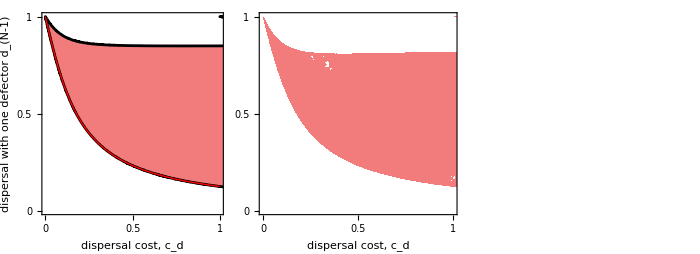

RegioPlots_Bvals.svg

```mathematica
GraphicsRow[{p2B,p3B,p5B},Spacings->1,ImageSize->700]
Export["RegioPlots_Bvals.svg",Show[%]]
```